# Setup

### goodlabel

```mathematica
goodlabel::usage="Evaluate[goodlabel[xlabel,ylabel, xstyle, ystyle]] makes plot labels with the desired style. Labels should be passed as strings.";
goodlabel[x_,y_]:={Frame->{{True,False},{True,False}},FrameLabel->{x,y}};
goodlabel[x_,y_,style_]:=goodlabel[x,y,style,style];goodlabel[x_,y_,xstyle_, ystyle_]:={Frame->{{True,False},{True,False}},FrameLabel->{Style[x,xstyle],Style[y,ystyle]}};
```

## sims

```mathematica
(* Note that scale parameter c in this data set represents the scale parameter for each of two lineages*)
```

```mathematica
sims = SemanticImport[FileNameJoin[{NotebookDirectory[],"MH_2D_discrete.txt"}]];
```

```mathematica
sims=sims[All,<|#,"dhomLow"->#hom-#homLow,"dhomHigh"->#homHigh-#hom|>&];
```

```mathematica
αlist = sims[All,#alpha&]//DeleteDuplicates//Normal//Sort;coallist = sims[All,#coal&]//DeleteDuplicates//Normal//Sort;
μlist = sims[All,#mu&]//DeleteDuplicates//Normal//Sort;
```

```mathematica
sims[All,#c&]
```

Dataset[<>]

```mathematica
sims[All,#mu&]
```

Dataset[<>]

```mathematica
μlist
```

{0.001,0.01,0.1,1.}

```mathematica
sims[All,#mu&]
```

Dataset[<>]

```mathematica
clist = sims[All,#c&]//DeleteDuplicates//Normal//Sort;
```

```mathematica
cdfsims = SemanticImport[FileNameJoin[{NotebookDirectory[],"CDF_data.txt"}]];
```

SemanticImport::nffil: File not found during SemanticImport.

```mathematica
cdfsims=cdfsims [All,<|#,"dcdfLow"->#cdf-#cdfLow,"dcdfHigh"->#cdfHigh-#cdf|>&];
```

## functions

```mathematica
fLT[x_,μ_, α_, Dα_]:=NIntegrate[(Cos[k x]/π)/(μ+ Dα k^α),{k,0,∞}];
fLT[x_,μ_, α_]:=fLT[x,μ,α,10^α];
```

```mathematica
coeff[c_,μ_,α_,Dα_]:=1/(2/c+(μ/Dα)^(1/α)/(α Sin[π/α]μ));
coeff[c_,μ_,α_]:=coeff[c,μ,α,10^α];
```

```mathematica
xscale[μ_,α_,Dα_]:=(Dα/μ)^(1/α);
xscale[μ_,α_]:=xscale[μ,α,10^α];
```

```mathematica
homscale[coal_,μ_,α_,Dα_]:=(1/π)/(Csc[π/α]/α+ 2 (Dα/μ)^(2/α)μ/coal);
homscale[coal_,μ_,α_]:=homscale[coal,μ,α,10^α/2];
```

```mathematica
approxhomscale[coal_,μ_,α_,Dα_]:=coal/(4*Pi(Dα/μ)^(2/α)μ);
approxhomscale[coal_,μ_,α_]:=approxhomscale[coal,μ,α,10^α];
```

```mathematica
Series[homscale[1/ρ,μ,α,Dα],{α,1,1}]
```

(α-1)+O[α-1]^2

```mathematica
xlist=10^Range[-14,8.5,.25];
```

```mathematica
xlist
```

{1.×10^-14,1.77828×10^-14,3.16228×10^-14,5.62341×10^-14,1.×10^-13,1.77828×10^-13,3.16228×10^-13,5.62341×10^-13,1.×10^-12,1.77828×10^-12,3.16228×10^-12,5.62341×10^-12,1.×10^-11,1.77828×10^-11,3.16228×10^-11,5.62341×10^-11,1.×10^-10,1.77828×10^-10,3.16228×10^-10,5.62341×10^-10,1.×10^-9,1.77828×10^-9,3.16228×10^-9,5.62341×10^-9,1.×10^-8,1.77828×10^-8,3.16228×10^-8,5.62341×10^-8,1.×10^-7,1.77828×10^-7,3.16228×10^-7,5.62341×10^-7,1.×10^-6,1.77828×10^-6,3.16228×10^-6,5.62341×10^-6,0.00001,0.0000177828,0.0000316228,0.0000562341,0.0001,0.000177828,0.000316228,0.000562341,0.001,0.00177828,0.00316228,0.00562341,0.01,0.0177828,0.0316228,0.0562341,0.1,0.177828,0.316228,0.562341,1.,1.77828,3.16228,5.62341,10.,17.7828,31.6228,56.2341,100.,177.828,316.228,562.341,1000.,1778.28,3162.28,5623.41,10000.,17782.8,31622.8,56234.1,100000.,177828.,316228.,562341.,1.×10^6,1.77828×10^6,3.16228×10^6,5.62341×10^6,1.×10^7,1.77828×10^7,3.16228×10^7,5.62341×10^7,1.×10^8,1.77828×10^8,3.16228×10^8}

```mathematica
αlistnew = {.5, 1.0, 1.25, 1.5, 2.0}
```

{0.5,1.,1.25,1.5,2.}

```mathematica
intvals=Quiet[Association@@Table[α->Association@@Table[x->NIntegrate[(k*BesselJ[0,k x]*Exp[-10^-16*k^2])/(1+k^α),{k,0,∞}],{x,xlist}],{α,αlistnew[[;;]]}]];
```

```mathematica
xmaxes=AssociationThread[αlistnew,{100000,100000,100000,100000,100000}];
```

# Plots

## α=0.5

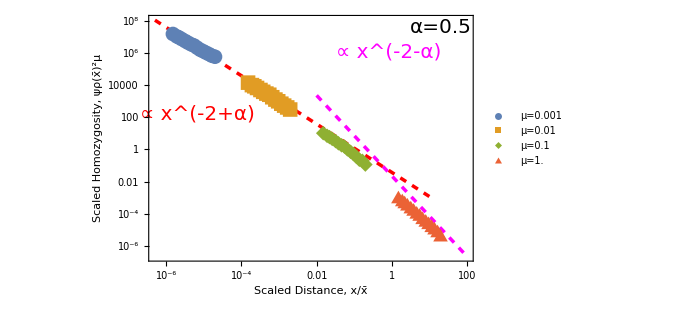

```mathematica
Module[{α=0.5,coal =1, plotpoints,μvals=μlist⟦1;;4⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha,  #c^#alpha],((4*Pi)^-1*Around[#hom,{#dhomLow, #dhomHigh}])/approxhomscale[#coal,#mu,#alpha, #c^#alpha]}&/@sims[Select[#alpha == α && #coal==coal &&#c == 10&& #mu ==μ&&#x0>0 &&#x0< 200&]],{μ,μvals}];
Show[
LogLogPlot[(0.724)*(2^-α*Gamma[α+1]/Gamma[α/2+1]^2)*Sin[Pi*α/2]*Gamma[ α/2+1]^2*(2^(1-α)*Pi^2)^-1*x^(-2-α),{x,.01,100},PlotStyle->{Magenta,Dashed,Thickness[.005]}], LogLogPlot[Gamma[ 1-α/2]*(Gamma[ α/2]*2^(α+1)*Pi)^-1*x^(-2+α),{x,.0000005,10},PlotStyle->{Red,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],
Epilog->{Text[Style["∝ x^(-2+α)",Red,20],Scaled[{.15,.6}]],Text[Style["∝ x^(-2-α)",Magenta,20],Scaled[{.74,.85}]],Text[Style["α=0.5",20],Scaled[{.9,.95}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, ψρ(x̄)^2μ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

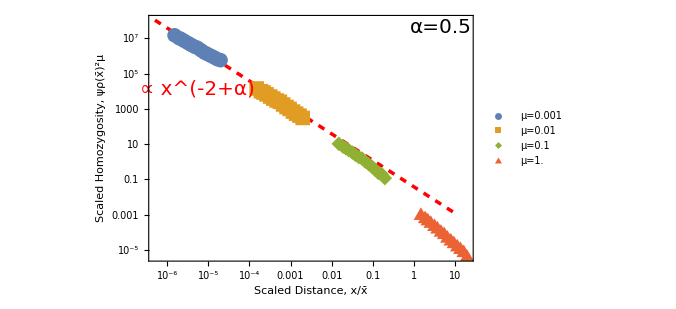

```mathematica
Module[{α=0.5,coal =1, plotpoints,μvals=μlist⟦1;;4⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha,  #c^#alpha],((4*Pi)^-1*Around[#hom,{#dhomLow, #dhomHigh}])/approxhomscale[#coal,#mu,#alpha,  #c^#alpha]}&/@sims[Select[#alpha == α && #coal==coal &&#c == 10&& #mu ==μ&&#x0>0 &&#x0<200&]],{μ,μvals}];
Show[
LogLogPlot[Gamma[ 1-α/2]*(Gamma[ α/2]*2^(α+1)*Pi)^-1*x^(-2+α),{x,.0000005,10},PlotStyle->{Red,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],
Epilog->{Text[Style["∝ x^(-2+α)",Red,20],Scaled[{.15,.7}]],Text[Style["α=0.5",20],Scaled[{.9,.95}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, ψρ(x̄)^2μ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

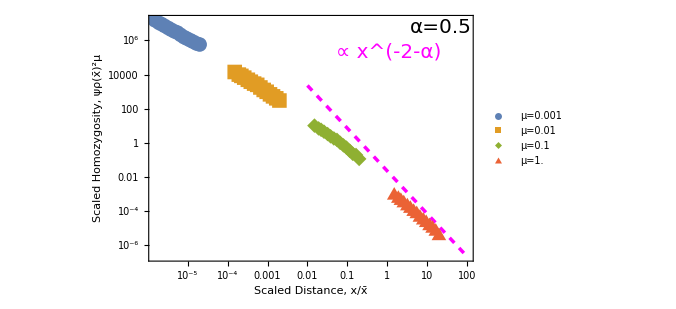

```mathematica
Module[{α=0.5,coal =1, plotpoints,μvals=μlist⟦1;;4⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha, #c^#alpha],((4*Pi)^-1*Around[#hom,{#dhomLow, #dhomHigh}])/approxhomscale[#coal,#mu,#alpha,  #c^#alpha]}&/@sims[Select[#alpha == α && #coal==coal &&#c == 10&& #mu ==μ&&#x0>0 &&#x0<220&]],{μ,μvals}];
Show[
LogLogPlot[(0.724)*(2^-α*Gamma[α+1]/Gamma[α/2+1]^2)*Sin[Pi*α/2]*Gamma[ α/2+1]^2*(2^(1-α)*Pi^2)^-1*x^(-2-α),{x,.01,100},PlotStyle->{Magenta,Dashed,Thickness[.005]}], ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],
Epilog->{Text[Style["∝ x^(-2-α)",Magenta,20],Scaled[{.74,.85}]],Text[Style["α=0.5",20],Scaled[{.9,.95}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, ψρ(x̄)^2μ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

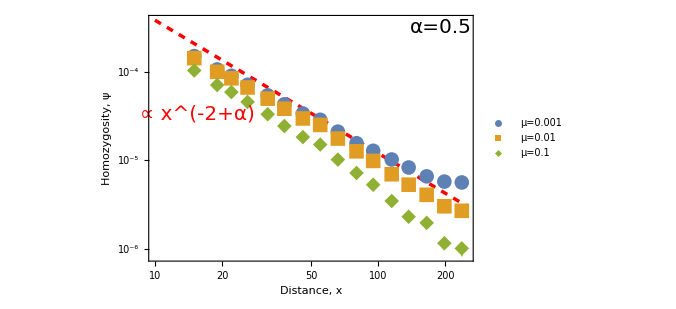

```mathematica
Module[{α=0.5,coal =1, plotpoints,μvals=μlist⟦1;;3⟧},plotpoints =Table[{#x0,Around[#hom,{#dhomLow, #dhomHigh}]}&/@sims[Select[#alpha == α && #coal==coal &&#c == 10&& #mu ==μ&&#x0>0&&#x0 < 250&]],{μ,μvals}];
Show[ LogLogPlot[coal*((10)^.5)^-1*Gamma[ 1-α/2]*(Gamma[ α/2]*2^(α+1)*Pi)^-1*x^(-2+α),{x,10,250},PlotStyle->{Red,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],
Epilog->{Text[Style["∝ x^(-2+α)",Red,20],Scaled[{.15,.6}]],Text[Style["α=0.5",20],Scaled[{.9,.95}]]},goodlabel["Distance, x"," Homozygosity, ψ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

```mathematica
Module[{α=0.5,coal =1, plotpoints,μvals=μlist⟦1;;3⟧},plotpoints =Table[{#x0,Around[#hom,{#dhomLow, #dhomHigh}]}&/@sims[Select[#alpha == α && #coal==coal &&#c == 10&& #mu ==μ&&#x0>0&&#x0 < 250&]],{μ,μvals}];
Show[ LogLogPlot[coal*(10^.5)^-1*Gamma[ 1-α/2]*(Gamma[ α/2]*2^(α+1)*Pi)^-1*x^(-2+α),{x,10,250},PlotStyle->{Red,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],
Epilog->{Text[Style["∝ x^(-2+α)",Red,20],Scaled[{.15,.6}]],Text[Style["α=0.5",20],Scaled[{.9,.95}]]},goodlabel["Distance, x","Homozygosity, ψ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

-Graphics-

## α=1.0

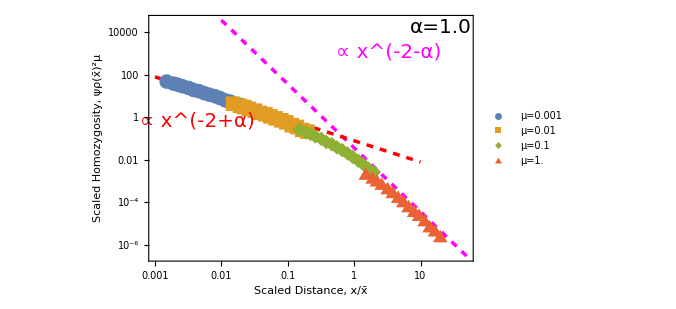

```mathematica
Module[{α=1.0,coal =1, plotpoints,μvals=μlist⟦1;;4⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha,  #c^#alpha],((4*Pi)^-1*Around[#hom,{#dhomLow, #dhomHigh}])/approxhomscale[#coal,#mu,#alpha,  #c^#alpha]}&/@sims[Select[#alpha == α && #coal==coal &&#c == 10&& #mu ==μ&&#x0>0 &&#x0<200&]],{μ,μvals}];
Show[
LogLogPlot[(0.724)*(2^-α*Gamma[α+1]/Gamma[α/2+1]^2)*Sin[Pi*α/2]*Gamma[ α/2+1]^2*(2^(1-α)*Pi^2)^-1*x^(-2-α),{x,.01,50},PlotStyle->{Magenta,Dashed,Thickness[.005]}], LogLogPlot[Gamma[ 1-α/2]*(Gamma[ α/2]*2^(α+1)*Pi)^-1*x^(-2+α),{x,.001,10},PlotStyle->{Red,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],
Epilog->{Text[Style["∝ x^(-2+α)",Red,20],Scaled[{.15,.57}]],Text[Style["∝ x^(-2-α)",Magenta,20],Scaled[{.74,.85}]],Text[Style["α=1.0",20],Scaled[{.9,.95}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, ψρ(x̄)^2μ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

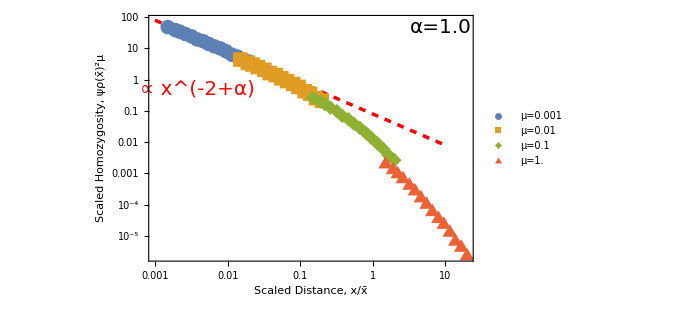

```mathematica
Module[{α=1.0,coal =1, plotpoints,μvals=μlist⟦1;;4⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha,  #c^#alpha],((4*Pi)^-1*Around[#hom,{#dhomLow, #dhomHigh}])/approxhomscale[#coal,#mu,#alpha,  #c^#alpha]}&/@sims[Select[#alpha == α && #coal==coal &&#c == 10&& #mu ==μ&&#x0>0 &&#x0<200&]],{μ,μvals}];
Show[
LogLogPlot[Gamma[ 1-α/2]*(Gamma[ α/2]*2^(α+1)*Pi)^-1*x^(-2+α),{x,.001,10},PlotStyle->{Red,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],
Epilog->{Text[Style["∝ x^(-2+α)",Red,20],Scaled[{.15,.7}]],Text[Style["α=1.0",20],Scaled[{.9,.95}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, ψρ(x̄)^2μ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

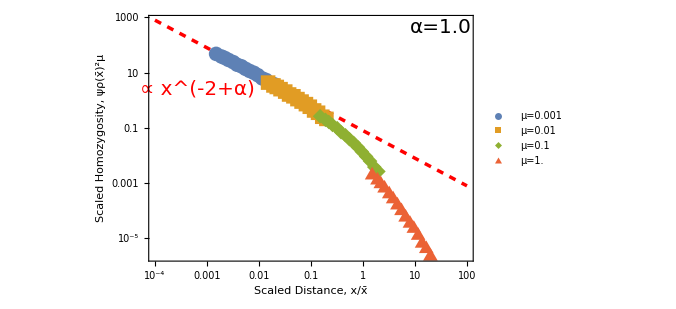

```mathematica
Module[{α=1.0,coal =1, plotpoints,μvals=μlist⟦1;;4⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha,  #c^#alpha],((4*Pi)^-1*Around[#hom,{#dhomLow, #dhomHigh}])/approxhomscale[#coal,#mu,#alpha,  #c^#alpha]}&/@sims[Select[#alpha == α && #coal==coal &&#c == 10&& #mu ==μ&&#x0>0 &&#x0<200&]],{μ,μvals}];
Show[
LogLogPlot[Gamma[ 1-α/2]*(Gamma[ α/2]*2^(α+1)*Pi)^-1*x^(-2+α),{x,.0001,100},PlotStyle->{Red,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],
Epilog->{Text[Style["∝ x^(-2+α)",Red,20],Scaled[{.15,.7}]],Text[Style["α=1.0",20],Scaled[{.9,.95}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, ψρ(x̄)^2μ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

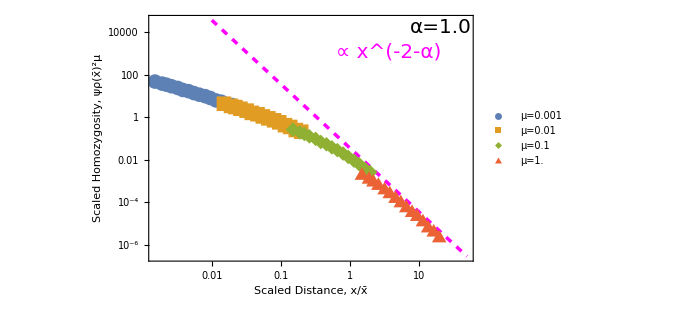

```mathematica
Module[{α=1.0,coal =1, plotpoints,μvals=μlist⟦1;;4⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha,  #c^#alpha],((4*Pi)^-1*Around[#hom,{#dhomLow, #dhomHigh}])/approxhomscale[#coal,#mu,#alpha,  #c^#alpha]}&/@sims[Select[#alpha == α && #coal==coal &&#c == 10&& #mu ==μ&&#x0>0 &&#x0<200&]],{μ,μvals}];
Show[
LogLogPlot[(0.724)*(2^-α*Gamma[α+1]/Gamma[α/2+1]^2)*Sin[Pi*α/2]*Gamma[ α/2+1]^2*(2^(1-α)*Pi^2)^-1*x^(-2-α),{x,.01,50},PlotStyle->{Magenta,Dashed,Thickness[.005]}], ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],
Epilog->{Text[Style["∝ x^(-2-α)",Magenta,20],Scaled[{.74,.85}]],Text[Style["α=1.0",20],Scaled[{.9,.95}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, ψρ(x̄)^2μ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

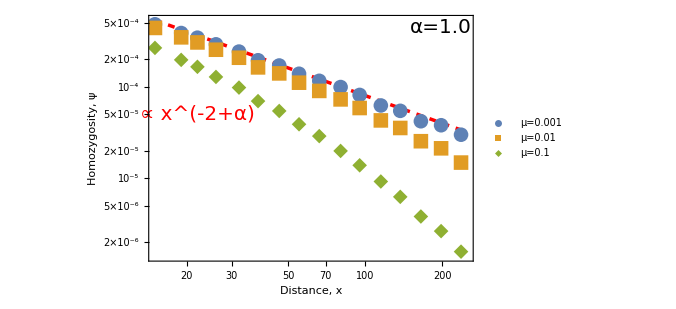

```mathematica
Module[{α=1.0,coal =1, plotpoints,μvals=μlist⟦1;;3⟧},plotpoints =Table[{#x0,Around[#hom,{#dhomLow, #dhomHigh}]}&/@sims[Select[#alpha == α && #coal==coal &&#c == 10&& #mu ==μ&&#x0>0&&#x0 < 250&]],{μ,μvals}];
Show[ LogLogPlot[coal*((10)^1)^-1*Gamma[ 1-α/2]*(Gamma[ α/2]*2^(α+1)*Pi)^-1*x^(-2+α),{x,15,250},PlotStyle->{Red,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],
Epilog->{Text[Style["∝ x^(-2+α)",Red,20],Scaled[{.15,.6}]],Text[Style["α=1.0",20],Scaled[{.9,.95}]]},goodlabel["Distance, x"," Homozygosity, ψ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

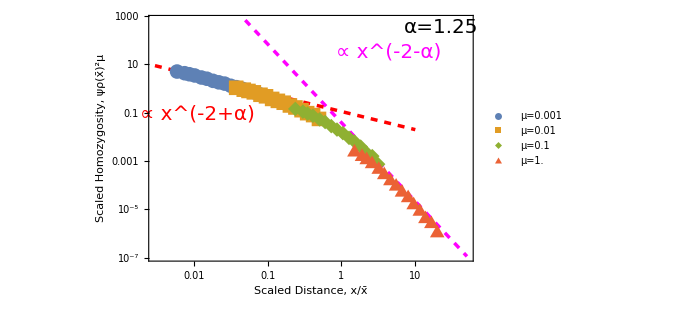

```mathematica
Module[{α=1.25,coal =1, plotpoints,μvals=μlist⟦1;;4⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha, #c^#alpha],((4*Pi)^-1*Around[#hom,{#dhomLow, #dhomHigh}])/approxhomscale[#coal,#mu,#alpha,  #c^#alpha]}&/@sims[Select[#alpha == α && #coal==coal &&#c == 10&& #mu ==μ&&#x0>0&& #x0 < 200& ]],{μ,μvals}];
Show[
LogLogPlot[(0.724)*(2^-α*Gamma[α+1]/Gamma[α/2+1]^2)*Sin[Pi*α/2]*Gamma[ α/2+1]^2*(2^(1-α)*Pi^2)^-1*x^(-2-α),{x,.05,50},PlotStyle->{Magenta,Dashed,Thickness[.005]}], LogLogPlot[Gamma[ 1-α/2]*(Gamma[ α/2]*2^(α+1)*Pi)^-1*x^(-2+α),{x,.003,10},PlotStyle->{Red,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],
Epilog->{Text[Style["∝ x^(-2+α)",Red,20],Scaled[{.15,.6}]],Text[Style["∝ x^(-2-α)",Magenta,20],Scaled[{.74,.85}]],Text[Style["α=1.25",20],Scaled[{.9,.95}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, ψρ(x̄)^2μ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

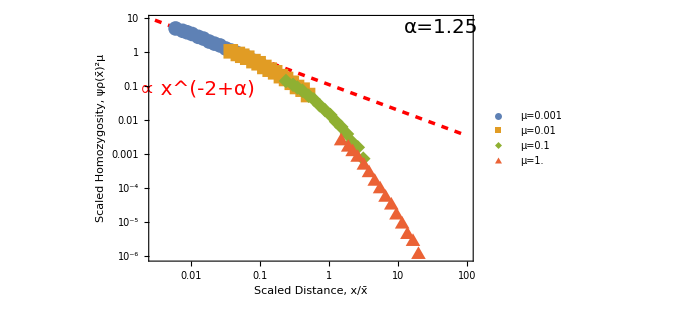

```mathematica
Module[{α=1.25,coal =1, plotpoints,μvals=μlist⟦1;;⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha,  #c^#alpha],((4*Pi)^-1*Around[#hom,{#dhomLow, #dhomHigh}])/approxhomscale[#coal,#mu,#alpha, #c^#alpha]}&/@sims[Select[#alpha == α && #coal==coal &&#c == 10&& #mu ==μ&&#x0>0&& #x0 < 200& ]],{μ,μvals}];
Show[
LogLogPlot[Gamma[ 1-α/2]*(Gamma[ α/2]*2^(α+1)*Pi)^-1*x^(-2+α),{x,.003,100},PlotStyle->{Red,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],
Epilog->{Text[Style["∝ x^(-2+α)",Red,20],Scaled[{.15,.7}]],Text[Style["α=1.25",20],Scaled[{.9,.95}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, ψρ(x̄)^2μ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

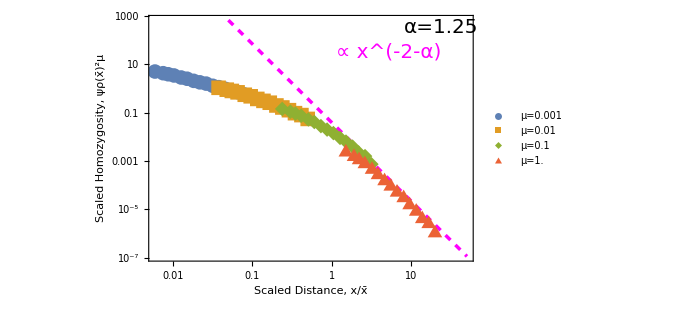

```mathematica
Module[{α=1.25,coal =1, plotpoints,μvals=μlist⟦1;;4⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha,  #c^#alpha],((4*Pi)^-1*Around[#hom,{#dhomLow, #dhomHigh}])/approxhomscale[#coal,#mu,#alpha,  #c^#alpha]}&/@sims[Select[#alpha == α && #coal==coal &&#c == 10&& #mu ==μ&&#x0>0&& #x0 < 200& ]],{μ,μvals}];
Show[
LogLogPlot[(0.724)*(2^-α*Gamma[α+1]/Gamma[α/2+1]^2)*Sin[Pi*α/2]*Gamma[ α/2+1]^2*(2^(1-α)*Pi^2)^-1*x^(-2-α),{x,.05,50},PlotStyle->{Magenta,Dashed,Thickness[.005]}], ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],
Epilog->{Text[Style["∝ x^(-2-α)",Magenta,20],Scaled[{.74,.85}]],Text[Style["α=1.25",20],Scaled[{.9,.95}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, ψρ(x̄)^2μ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

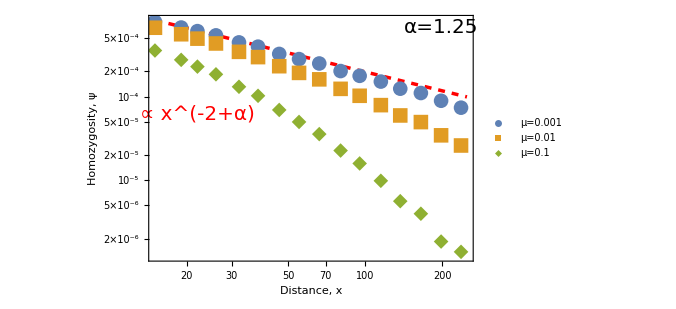

```mathematica
Module[{α=1.25,coal =1, plotpoints,μvals=μlist⟦1;;3⟧},plotpoints =Table[{#x0,Around[#hom,{#dhomLow, #dhomHigh}]}&/@sims[Select[#alpha == α && #coal==coal &&#c == 10&& #mu ==μ&&#x0>0&&#x0 < 250&]],{μ,μvals}];
Show[ LogLogPlot[coal*((10)^1.25)^-1*Gamma[ 1-α/2]*(Gamma[ α/2]*2^(α+1)*Pi)^-1*x^(-2+α),{x,15,250},PlotStyle->{Red,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],
Epilog->{Text[Style["∝ x^(-2+α)",Red,20],Scaled[{.15,.6}]],Text[Style["α=1.25",20],Scaled[{.9,.95}]]},goodlabel["Distance, x"," Homozygosity, ψ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

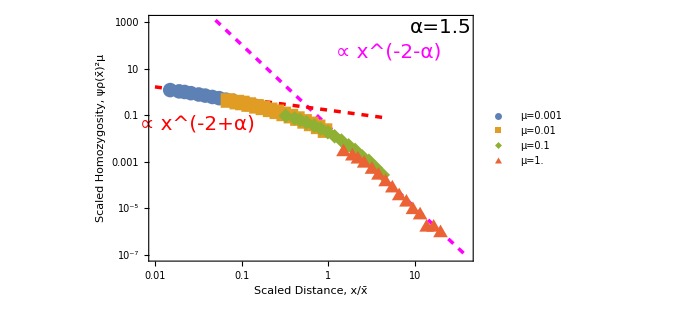

```mathematica
Module[{α=1.5,coal =1, plotpoints,μvals=μlist⟦1;;4⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha,  #c^#alpha],((4*Pi)^-1*Around[#hom,{#dhomLow, #dhomHigh}])/approxhomscale[#coal,#mu,#alpha,  #c^#alpha]}&/@sims[Select[#alpha == α && #coal==coal &&#c == 10&& #mu ==μ&&#x0>0&& #x0 < 200& ]],{μ,μvals}];
Show[
LogLogPlot[(0.724)*(2^-α*Gamma[α+1]/Gamma[α/2+1]^2)*Sin[Pi*α/2]*Gamma[ α/2+1]^2*(2^(1-α)*Pi^2)^-1*x^(-2-α),{x,.05,40},PlotStyle->{Magenta,Dashed,Thickness[.005]}], LogLogPlot[Gamma[ 1-α/2]*(Gamma[ α/2]*2^(α+1)*Pi)^-1*x^(-2+α),{x,.01,5},PlotStyle->{Red,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],
Epilog->{Text[Style["∝ x^(-2+α)",Red,20],Scaled[{.15,.56}]],Text[Style["∝ x^(-2-α)",Magenta,20],Scaled[{.74,.85}]],Text[Style["α=1.5",20],Scaled[{.9,.95}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, ψρ(x̄)^2μ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

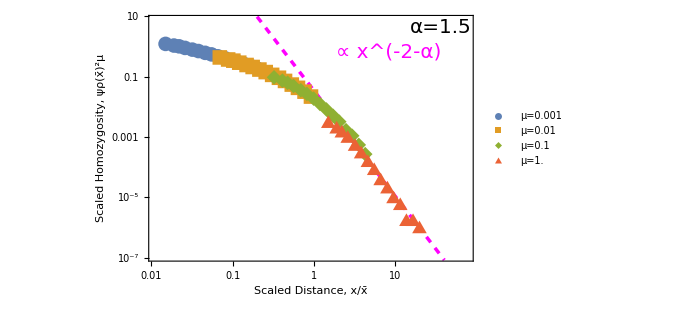

```mathematica
Module[{α=1.5,coal =1, plotpoints,μvals=μlist⟦1;;4⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha, #c^#alpha],((4*Pi)^-1*Around[#hom,{#dhomLow, #dhomHigh}])/approxhomscale[#coal,#mu,#alpha, #c^#alpha]}&/@sims[Select[#alpha == α && #coal==coal &&#c == 10&& #mu ==μ&&#x0>0&& #x0 < 200& ]],{μ,μvals}];
Show[
LogLogPlot[(0.724)*(2^-α*Gamma[α+1]/Gamma[α/2+1]^2)*Sin[Pi*α/2]*Gamma[ α/2+1]^2*(2^(1-α)*Pi^2)^-1*x^(-2-α),{x,.2,40},PlotStyle->{Magenta,Dashed,Thickness[.005]}], ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.25}]],
Epilog->{Text[Style["∝ x^(-2-α)",Magenta,20],Scaled[{.74,.85}]],Text[Style["α=1.5",20],Scaled[{.9,.95}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, ψρ(x̄)^2μ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->{{-4.5,4.33},{-16,2}},Axes->False]]
```

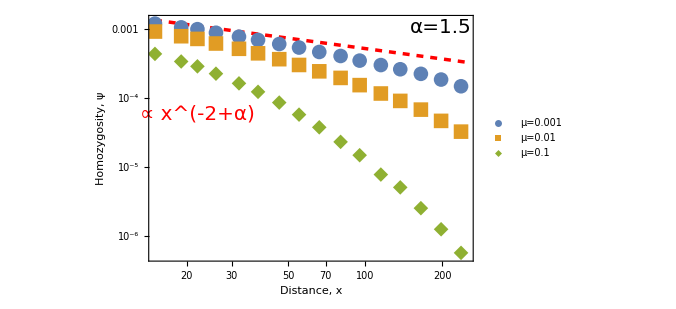

```mathematica
Module[{α=1.5,coal =1, plotpoints,μvals=μlist⟦1;;3⟧},plotpoints =Table[{#x0,Around[#hom,{#dhomLow, #dhomHigh}]}&/@sims[Select[#alpha == α && #coal==coal &&#c == 10&& #mu ==μ&&#x0>0&&#x0 < 250&]],{μ,μvals}];
Show[ LogLogPlot[coal*((10)^1.5)^-1*Gamma[ 1-α/2]*(Gamma[ α/2]*2^(α+1)*Pi)^-1*x^(-2+α),{x,15,250},PlotStyle->{Red,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],
Epilog->{Text[Style["∝ x^(-2+α)",Red,20],Scaled[{.15,.6}]],Text[Style["α=1.5",20],Scaled[{.9,.95}]]},goodlabel["Distance, x"," Homozygosity, ψ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

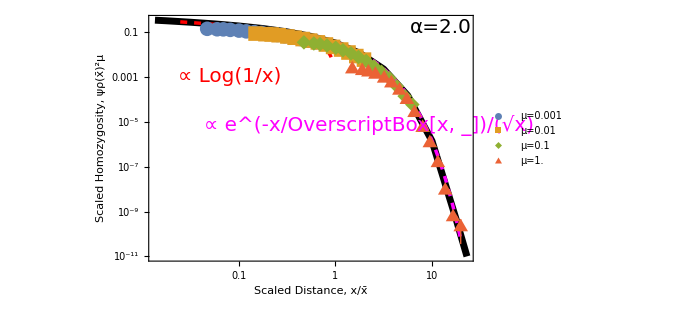

```mathematica
Module[{α=2.0,coal =1, plotpoints,μvals=μlist⟦1;;4⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha, #c^#alpha],((4*Pi)^-1*Around[#hom,{#dhomLow, #dhomHigh}])/approxhomscale[#coal,#mu,#alpha, #c^#alpha]}&/@sims[Select[#alpha == α && #coal==coal &&#c == 10&& #mu ==μ&&#x0>0 &&#x0<200&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,(4*Pi)^-1*intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]}
,PlotRange->{{10^-3,10000},{10^-11,.35}}],
LogLogPlot[(4*Sqrt[2*Pi])^-1*Exp[-x]/Sqrt[x],{x,1,20},PlotStyle->{Magenta,Dashed,Thickness[.005]}], LogLogPlot[(4*Pi)^-1*Log[1/x],{x,.025,100000},PlotStyle->{Red,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],
Epilog->{Text[Style["∝ Log(1/x)",Red,20],Scaled[{.25,.75}]],Text[Style["∝ e^(-x/OverscriptBox[x, _])/(√x)",Magenta,20],Scaled[{.68,.55}]],Text[Style["α=2.0",20],Scaled[{.9,.95}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, ψρ(x̄)^2μ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

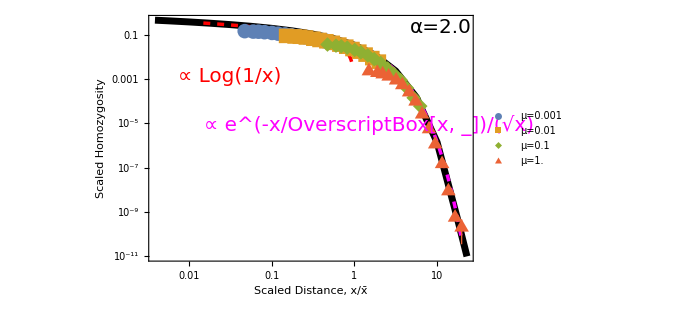

```mathematica
Module[{α=2.0,coal =1, plotpoints,μvals=μlist⟦1;;4⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha, #c^#alpha],((4*Pi)^-1*Around[#hom,{#dhomLow, #dhomHigh}])/approxhomscale[#coal,#mu,#alpha, #c^#alpha]}&/@sims[Select[#alpha == α && #coal==coal &&#c == 10&& #mu ==μ&&#x0>0 &&#x0<200&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,(4*Pi)^-1*intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]}
,PlotRange->{{10^-3,10000},{10^-11,.45}}],
LogLogPlot[(4*Sqrt[2*Pi])^-1*Exp[-x]/Sqrt[x],{x,1,20},PlotStyle->{Magenta,Dashed,Thickness[.005]}], LogLogPlot[(4*Pi)^-1*Log[1/x],{x,.015,100000},PlotStyle->{Red,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],
Epilog->{Text[Style["∝ Log(1/x)",Red,20],Scaled[{.25,.75}]],Text[Style["∝ e^(-x/OverscriptBox[x, _])/(√x)",Magenta,20],Scaled[{.68,.55}]],Text[Style["α=2.0",20],Scaled[{.9,.95}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

```mathematica
(*For alpha = 2.05, difference between (c^2) and ω^α is factor of (Sqrt[2*(α-2)*(α-1)/(α^2)])^α*)
```

```mathematica
(*Extra factor of two for long distance expression since we draw from fisher dist for each lineage, i.e. prefactor is 2 ω^α in power law*)
```

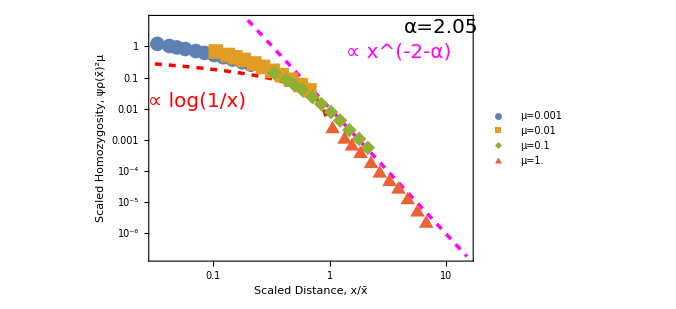

```mathematica
Module[{α=2.05,coal =1, plotpoints,μvals=μlist⟦1;;4⟧},plotpoints =Table[{(#x0)/xscale[#mu,2.0, (#c)^2.00],((4*Pi)^-1*Around[#hom,{#dhomLow, #dhomHigh}])/approxhomscale[#coal,#mu,2.0, (#c)^2.00]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0 && #x0<100&]],{μ,μvals}];
Show[LogLogPlot[(200)^(-.05/2.05)*(0.724)*2*(2*Pi)^-1*(1/4)*(Sqrt[2*(α-2)*(α-1)/(α^2)])^α*(1/α)^(-1-α)*x^(-2-α),{x,.2,15},PlotStyle->{Magenta,Dashed,Thickness[.005]}], LogLogPlot[(4*Pi)^-1 Log[1/x],{x,.032,1000},PlotStyle->{Red,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],
Epilog->{Text[Style["∝ log(1/x)",Red,20],Scaled[{.15,.65}]],Text[Style["∝ x^(-2-α)",Magenta,20],Scaled[{.77,.85}]],Text[Style["α=2.05",20],Scaled[{.9,.95}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, ψρ(x̄)^2μ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

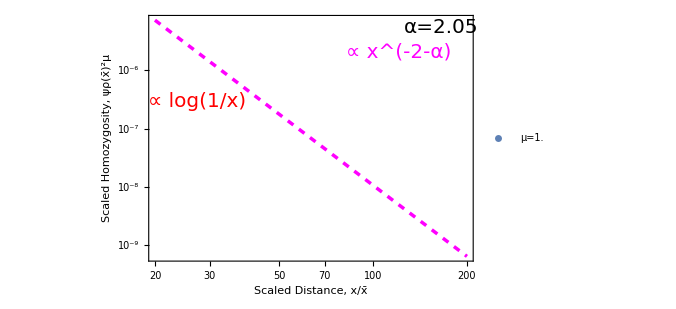

```mathematica
Module[{α=2.05,coal =1, plotpoints,μvals=μlist⟦4;;4⟧},plotpoints =Table[{#x0,Around[#hom,{#dhomLow, #dhomHigh}]}&/@sims[Select[#alpha == α && #coal==coal &&#c == 10&& #mu ==μ&&#x0>0 && #x0<160&]],{μ,μvals}];
Show[LogLogPlot[(0.724)*(2*Pi)^-1*(1/4)*(200)^(2.05/2)*(Sqrt[2*(α-2)*(α-1)/(α^2)])^α*(1/α)^(-1-α)*x^(-2-α),{x,20,200},PlotStyle->{Magenta,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],
Epilog->{Text[Style["∝ log(1/x)",Red,20],Scaled[{.15,.65}]],Text[Style["∝ x^(-2-α)",Magenta,20],Scaled[{.77,.85}]],Text[Style["α=2.05",20],Scaled[{.9,.95}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, ψρ(x̄)^2μ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

```mathematica
`
```

```mathematica
(*For alpha = 2.05, difference between (c^2/2)^α and ω^α is factor of (Sqrt[2*(α-2)*(α-1)/(α^2)])^α*)
```

```mathematica
Simplify[a^3/((a-1)^2*(a-2)) + a^2/(a-1)^2]
```

(2 a^2)/(2-3 a+a^2)

```mathematica
(*add variance and mean^2 of one sided fisher distribution to get variance of two sided*)
```

```mathematica
FullSimplify[2*(2a)^2*(2 + 2a -2)/(2*(2*a-2)^2*(2*a-4)) + (2*a)^2/(2*a-2)^2]
```

(2 a^2)/(2-3 a+a^2)

```mathematica
FullSimplify[(2 a^2)/(2-3 a+a^2) - (2 a^2)/((a-2)*(a-1))]
```

0

```mathematica
Simplify[2*(2a)^2*(2 + 2a -2)/(2*(2*a-2)^2*(2*a-4))]
```

a^3/((-2+a) (-1+a)^2)

```mathematica
(4*Pi)^-1 InverseHankelTransform[
Abs[k]^(-a),k,x]
```

(2^(-1-a) x^(-2+a) Gamma[1-a/2])/(π Gamma[a/2])

```mathematica
4*N[Sum[n*Exp[-2*n],{n,1,1Infinity}]]
```

0.724062

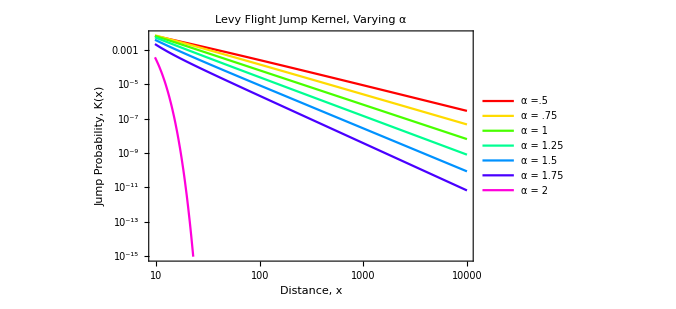

```mathematica
Show[LogLogPlot[Table[PDF[StableDistribution[0,α,0,0,2],x],{α,{.5,.75,1,1.25,1.5, 1.75,2}}]//Evaluate,{x,0,10000}, PlotStyle->Table[Hue[h-.1,1,1],{h,.1,1.1-1/7,1/7}] , LabelStyle->Directive[Bold, Black], PlotLabel -> Style["Levy Flight Jump Kernel, Varying α", FontSize -> 24], PlotLegends->{"α =.5","α = .75","α = 1","α =  1.25","α = 1.5","α = 1.75","α = 2"}, Frame->True,FrameLabel->{"xlabel","ylabel"},FrameStyle->{{None,Black},{None,Black}}],goodlabel["Distance, x","Jump Probability, K(x)",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]
```

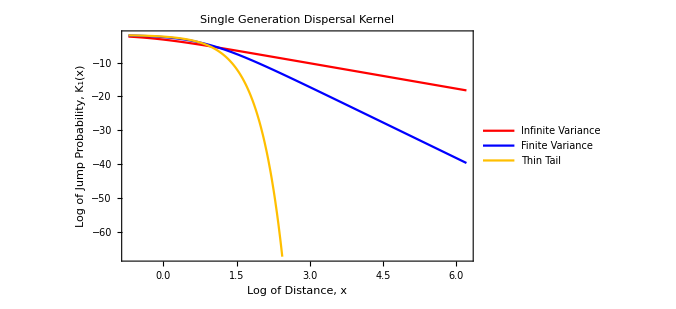

```mathematica
Show[LogLogPlot[Table[PDF[MultivariateTDistribution[{{1,0},{0,1}},α],{x,0}],{α,{.5, 5.0, 1000000}}]//Evaluate,{x,0,500}, PlotStyle->{Red, Blue, RGBColor[1,.75,0]} , LabelStyle->Directive[Bold, Black], PlotLabel -> Style["Single Generation Dispersal Kernel", FontSize -> 24], PlotLegends->Placed[LineLegend[{Red, Blue, RGBColor[1,.75,0]},{"Infinite Variance","Finite Variance","Thin Tail"}],{.2,.5}], Frame->True,FrameLabel->{"xlabel","ylabel"},Ticks->{None,None},FrameTicks->{None,None},FrameTicksStyle->Directive[FontOpacity->0,FontSize->0],FrameStyle->{{None,Black},{None,Black}}],goodlabel["Log of Distance, x","Log of Jump Probability, K_1(x)",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]
```

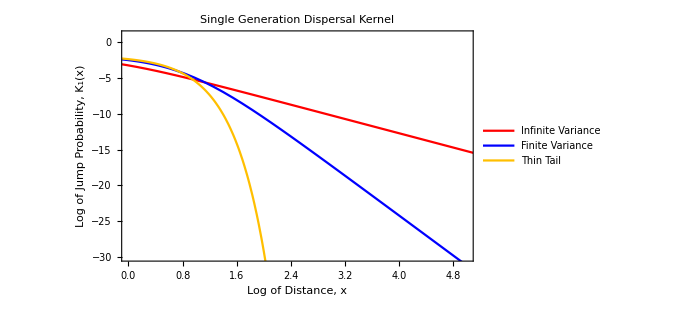

```mathematica
Show[LogLogPlot[Table[PDF[MultivariateTDistribution[{{1,0},{0,1}},α],{x,0}],{α,{.5, 5.0, 1000000}}]//Evaluate,{x,0,500}, PlotStyle->{Red, Blue, RGBColor[1,.75,0]} , LabelStyle->Directive[Bold, Black], PlotLabel -> Style["Single Generation Dispersal Kernel", FontSize -> 24], PlotLegends->Placed[LineLegend[{Red, Blue, RGBColor[1,.75,0]},{"Infinite Variance","Finite Variance","Thin Tail"}],{.15,.3}], Frame->True,FrameLabel->{"xlabel","ylabel"},Ticks->{None,None},FrameTicks->{None,None},FrameTicksStyle->Directive[FontOpacity->0,FontSize->0],FrameStyle->{{None,Black},{None,Black}}],goodlabel["Log of Distance, x","Log of Jump Probability, K_1(x)",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->{{0,5},{-30, 1}},Axes->False]
```

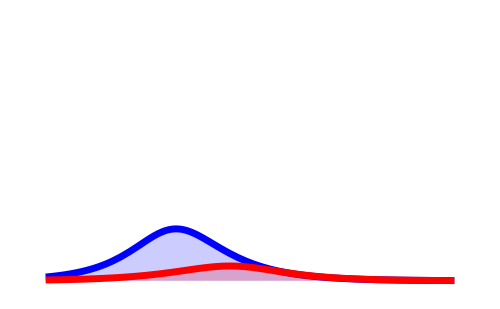

```mathematica
Show[LogLinearPlot[Table[.12*PDF[StableDistribution[0,α,0,0,t],2],{α,{1.1}}]//Evaluate,{t,.1,1000}, PlotStyle->{Blue,Thickness[.01]} , LabelStyle->Directive[Bold, Black], PlotRange->{{.1,1000},{.000, .05}}, Filling -> Axis],LogLinearPlot[Table[.12*PDF[StableDistribution[0,α,0,0,t],6],{α,{0.9}}]//Evaluate,{t,.1,1000}, PlotStyle->{Red,Thickness[.01]} ,LabelStyle->Directive[Bold, Black], PlotRange->{{1,1000},{.000, .1}}, Filling -> Axis],FrameStyle->Directive[20,Black],FrameTicksStyle->Directive[FontOpacity->0,FontSize->0], ImageSize->500,
Axes->False]
```

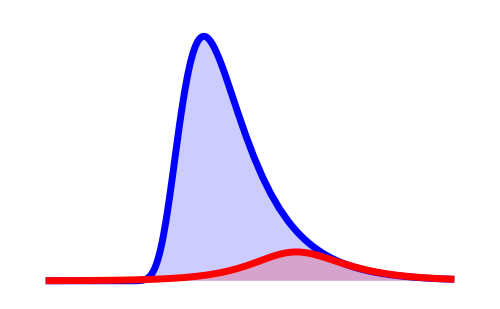

```mathematica
Show[LogLinearPlot[Table[PDF[StableDistribution[0,α,0,0,t],5],{α,{2.0}}]//Evaluate,{t,.1,1000}, PlotStyle->{Blue,Thickness[.01]} , LabelStyle->Directive[Bold, Black], PlotRange->{{.1,1000},{.0000, .05}}, Filling -> Axis],LogLinearPlot[Table[PDF[StableDistribution[0,α,0,0,t],30],{α,{1.1}}]//Evaluate,{t,.1,1000}, PlotStyle->{Red,Thickness[.01]} ,LabelStyle->Directive[Bold, Black], PlotRange->{{1,1000},{.0000, .1}},Filling -> Axis],FrameTicksStyle->Directive[FontOpacity->0,FontSize->0], ImageSize->500,Axes->False]
```

General::munfl: Exp[-39985.] is too small to represent as a normalized machine number; precision may be lost.

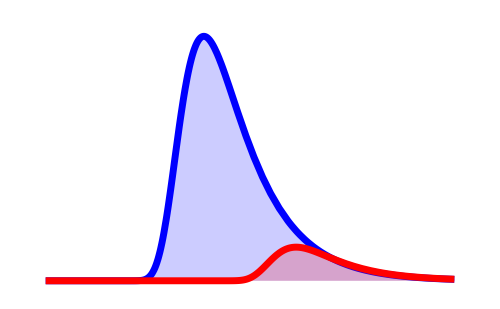

```mathematica
Show[LogLinearPlot[Table[PDF[StableDistribution[0,α,0,0,t],5],{α,{2.0}}]//Evaluate,{t,.1,1000}, PlotStyle->{Blue,Thickness[.01]} , LabelStyle->Directive[Bold, Black], PlotRange->{{.1,1000},{0, .05}},Filling -> Axis],LogLinearPlot[Table[1.1*PDF[StableDistribution[0,α,0,0,t],40],{α,{2.0}}]//Evaluate,{t,.1,1000}, PlotStyle->{Red,Thickness[.01]} ,LabelStyle->Directive[Bold, Black], PlotRange->{{1,1000},{0, .1}},Filling -> Axis],FrameTicksStyle->Directive[FontOpacity->0,FontSize->0], ImageSize->500,Axes->False]
```

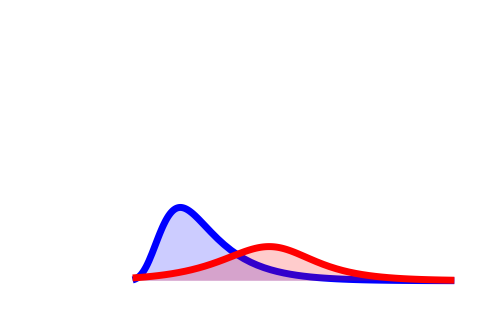

```mathematica
Show[LogLinearPlot[Table[2.5*.12*PDF[StableDistribution[0,α,0,0,t],5],{α,{2.0}}]//Evaluate,{t,1.0,5000}, PlotStyle->{Blue,Thickness[.01]} , LabelStyle->Directive[Bold, Black], PlotRange->{{.1,5000},{.000, .05}}, Filling -> Axis],LogLinearPlot[Table[1.8*7.5*.12*PDF[StableDistribution[0,α,0,0,t],35],{α,{0.9}}]//Evaluate,{t,1.0,5000}, PlotStyle->{Red,Thickness[.01]} ,LabelStyle->Directive[Bold, Black], PlotRange->{{.1,5000},{.000, .1}}, Filling -> Axis],FrameStyle->Directive[20,Black],FrameTicksStyle->Directive[FontOpacity->0,FontSize->0], ImageSize->500,
Axes->False]
```

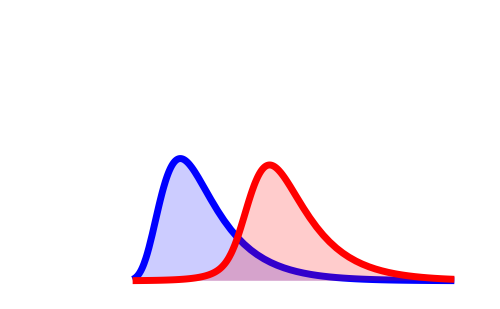

```mathematica
Show[LogLinearPlot[Table[.5*PDF[StableDistribution[0,α,0,0,t],5],{α,{2.0}}]//Evaluate,{t,1.0,5000}, PlotStyle->{Blue,Thickness[.01]} , LabelStyle->Directive[Bold, Black], PlotRange->{{.1,5000},{.0000, .05}}, Filling -> Axis],LogLinearPlot[Table[5.1*PDF[StableDistribution[0,α,0,0,t],50],{α,{1.7}}]//Evaluate,{t,1.0,5000}, PlotStyle->{Red,Thickness[.01]} ,LabelStyle->Directive[Bold, Black], PlotRange->{{1,5000},{.0000, .1}},Filling -> Axis],FrameTicksStyle->Directive[FontOpacity->0,FontSize->0], ImageSize->500,Axes->False]
```

General::munfl: Exp[-899.687] is too small to represent as a normalized machine number; precision may be lost.

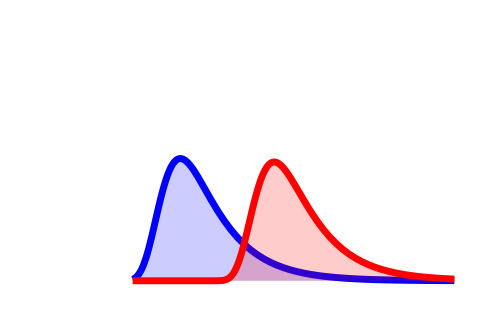

```mathematica
Show[LogLinearPlot[Table[.50*PDF[StableDistribution[0,α,0,0,t],5],{α,{2.0}}]//Evaluate,{t,1,5000}, PlotStyle->{Blue,Thickness[.01]} , LabelStyle->Directive[Bold, Black], PlotRange->{{.1,5000},{0, .05}},Filling -> Axis],LogLinearPlot[Table[5.3*1.1*PDF[StableDistribution[0,α,0,0,t],60],{α,{2.0}}]//Evaluate,{t,1,5000}, PlotStyle->{Red,Thickness[.01]} ,LabelStyle->Directive[Bold, Black], PlotRange->{{1,5000},{0, .1}},Filling -> Axis],FrameTicksStyle->Directive[FontOpacity->0,FontSize->0], ImageSize->500,Axes->False]
```

# 2D Asymptotics

```mathematica
(*These are expressions for ψ(x)/(1-ψ(0)) *)
```

## x << δ

```mathematica
(4*Pi*ρ*D)^-1*Integrate[k*Exp[-k^2*delta^2/2]/( k^a),{k,0,Infinity}, Assumptions->{x > 0, delta > 0, a > 0}]
```

ConditionalExpression[(2^(-2-a/2) delta^(-2+a) Gamma[1-a/2])/(D π ρ),a<2]

## δ << x << x̄

```mathematica
(4*Pi*ρ*D)^-1*InverseHankelTransform[
Abs[k]^(-a),k,x]
```

(2^(-1-a) x^(-2+a) Gamma[1-a/2])/(D π ρ Gamma[a/2])

## x >> x̄

```mathematica
(4*Pi*ρ*mu*xbar^2)^-1*xbar^(a+2)*InverseHankelTransform[
Abs[k]^(a),k,x]
```

(2^(-1+a) x^(-2-a) xbar^a Gamma[1+a/2])/(mu π ρ Gamma[-a/2])

```mathematica
(*Note that xbar = (D/mu)^(1/a)*)
```